Anya Johnson and Neem Serra

## One Resource, One Species, Fixed Yield

### Consider the model for one species in a chemostat with one limiting resource that we studied in class. dR/dt=a(R_in-R)-v_max R/(R+K)P dP/dt=Yv_max R/(R+K)P-mP

### Either by hand or with Mathematica's help, investigate this model's equilibria and their stability.

```mathematica
f1:=a(rin-r) -vmax(r/(r+k))p;
f2:=y*vmax(r/(r+k))p-m*p;
eq = Solve[{f1==0, f2==0}, {r, p}]
```

{{r→rin,p→0},{r→-(k m)/(m-vmax y),p→-(a y (-k m-m rin+rin vmax y))/(m (m-vmax y))}}

```mathematica
(* jacobian matrix*)
j := D[{f1, f2}, {{r, p}}];
j // MatrixForm
```

(-a+(p r vmax)/(k+r)^2-(p vmax)/(k+r) | -(r vmax)/(k+r)
-(p r vmax y)/(k+r)^2+(p vmax y)/(k+r) | -m+(r vmax y)/(k+r))

```mathematica
j/.eq[[1]] // MatrixForm
Eigenvalues[j/.eq[[1]]]
```

(-a | -(rin vmax)/(k+rin)
0 | -m+(rin vmax y)/(k+rin))

{-a,-m+(rin vmax y)/(k+rin)}

This equlibira will be unstable if there are more per capita births than deaths. Otherwise it will be stable, because a is always positive.

```mathematica
j/.eq[[2]] // MatrixForm
Eigenvalues[j/.eq[[2]]]
```

(-a+(a k vmax y (-k m-m rin+rin vmax y))/((m-vmax y)^2 (k-(k m)/(m-vmax y))^2)+(a vmax y (-k m-m rin+rin vmax y))/(m (m-vmax y) (k-(k m)/(m-vmax y))) | (k m vmax)/((m-vmax y) (k-(k m)/(m-vmax y)))
-(a k vmax y^2 (-k m-m rin+rin vmax y))/((m-vmax y)^2 (k-(k m)/(m-vmax y))^2)-(a vmax y^2 (-k m-m rin+rin vmax y))/(m (m-vmax y) (k-(k m)/(m-vmax y))) | -m-(k m vmax y)/((m-vmax y) (k-(k m)/(m-vmax y))))

{1/(2 k m vmax y)(-a k m^2-a m^2 rin+2 a m rin vmax y-a rin vmax^2 y^2-√((a k m^2+a m^2 rin-2 a m rin vmax y+a rin vmax^2 y^2)^2-4 k m vmax y (a k m^3+a m^3 rin-a k m^2 vmax y-2 a m^2 rin vmax y+a m rin vmax^2 y^2))),1/(2 k m vmax y)(-a k m^2-a m^2 rin+2 a m rin vmax y-a rin vmax^2 y^2+√((a k m^2+a m^2 rin-2 a m rin vmax y+a rin vmax^2 y^2)^2-4 k m vmax y (a k m^3+a m^3 rin-a k m^2 vmax y-2 a m^2 rin vmax y+a m rin vmax^2 y^2)))}

### Plot the growth rate vs R and calculate R* using the species parameters below. μ: green, m: red.

```mathematica
vmax=2;
k=1;
y=1;
m=1;
```

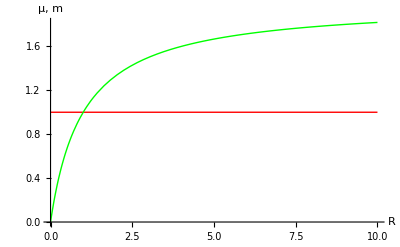

```mathematica
Plot[{m,y*vmax*r/(r+k)},{r,0,10},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0]},AxesLabel->{"R","μ, m"}]
```

```mathematica
Solve[1== y*vmax*r/(r+k)]
```

{{r→1}}

### Numerically solve the model using the species parameters above and the chemostat parameters below. Try a nutrient inflow concentration, Rin, below and above R*. What happens in each case? Compare the growth of biomass with the logistic equation. R: blue, N: green.

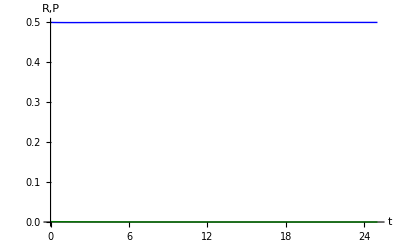

```mathematica
a=1;
rin=.5;

tmax=25;

sol=NDSolve[{
r'[t]==a*(rin-r[t])-vmax*r[t]/(r[t]+k)*p[t],
p'[t]==y*vmax*r[t]/(r[t]+k)*p[t]-m*p[t],
r[0]==rin,p[0]==0.001},{r,p},{t,0,tmax}];

Plot[Evaluate[{r[t],p[t]}/.sol],{t,0,tmax},PlotStyle->{RGBColor[0,0,1],RGBColor[0,1,0]},AxesLabel->{"t","R,P"}]
```

If the resource input is below R*, the species dies out and the resource remains at a constant rate. If the resource input is above R* the species brings the resource down to R* and grows to carrying capacity.

## One Resource, Two Species Competition, Fixed Yields

### Now consider competition of two species in a chemostat with one limiting resource. dR/dt=a(R_in-R)-v_max1 R/(R+K_1)P_1-v_max2 R/(R+K_2)P_2 dP_1/dt=Y_1v_max1 R/(R+K_1)P_1-m_1 P_1 dP_2/dt=Y_2v_max2 R/(R+K_2)P_2-m_2 P_2

### Plot the growth rate vs R and calculate R* using the parameters for both species below. Which species grows faster at high resource levels? Which species is the better competitor at equilibrium? μ1: light green, μ2: dark green, m: red.

```mathematica
vmax1=2;
k1=1;
y1=1;
m1=1;

vmax2=3;
k2=4;
y2=1;
m2=1;
```

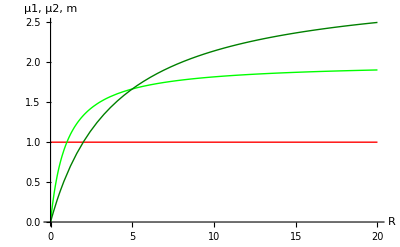

```mathematica
Plot[{m1,y1*vmax1*r/(r+k1),y2*vmax2*r/(r+k2)},{r,0,20},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0.5,0]},AxesLabel->{"R","μ1, μ2, m"}]
```

Dark green does best at higher resource levels, and as the resource is brought down, light green becomes the better competitor at equilibrium, as it has a lower R*.

```mathematica
Solve[1== y1*vmax1*r/(r+k1)]
```

{{r→1}}

```mathematica
Solve[1 == y2*vmax2*r/(r+k2)]
```

{{r→2}}

Species 1’s R* is 1, and species 2’s R* is 2.

### Numerically solve the model using the species parameters above and the chemostat parameters below. Does the outcome agree with your expectations? R: blue, N1: light green, N2: dark green.

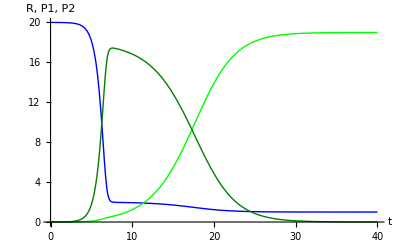

```mathematica
a=1;
rin=20;

tmax=40;

sol=NDSolve[{
r'[t]==a*(rin-r[t])-vmax1*r[t]/(r[t]+k1)*p1[t]-vmax2*r[t]/(r[t]+k2)*p2[t],
p1'[t]==y1*vmax1*r[t]/(r[t]+k1)*p1[t]-m1*p1[t],
p2'[t]==y2*vmax2*r[t]/(r[t]+k2)*p2[t]-m2*p2[t],
r[0]==rin,p1[0]==0.001,p2[0]==0.001},{r,p1,p2},{t,0,tmax}];

Plot[Evaluate[{r[t],p1[t],p2[t]}/.sol],{t,0,tmax},PlotStyle->{RGBColor[0,0,1],RGBColor[0,1,0],RGBColor[0,0.5,0]},AxesLabel->{"t","R, P1, P2"}]
```

Yes, because dark green does better at high resource levels, it initially increasing, but as resource levels drop, light green is able to exclude dark green.

### Can you adjust the values of m (leave m1=m2=m so that both species have the same mortaliy rate) to change the outcome of competition? What might the ecological implication of this be? Can you solve for the value of m where this switch should occur?

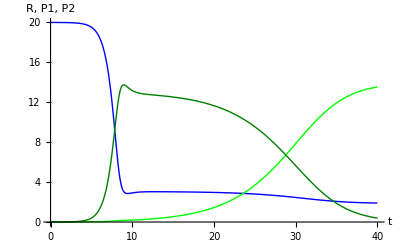

```mathematica
a=1;
rin=20;
m1 = 1.3;
m2 = 1.3;

tmax=40;

sol=NDSolve[{
r'[t]==a*(rin-r[t])-vmax1*r[t]/(r[t]+k1)*p1[t]-vmax2*r[t]/(r[t]+k2)*p2[t],
p1'[t]==y1*vmax1*r[t]/(r[t]+k1)*p1[t]-m1*p1[t],
p2'[t]==y2*vmax2*r[t]/(r[t]+k2)*p2[t]-m2*p2[t],
r[0]==rin,p1[0]==0.001,p2[0]==0.001},{r,p1,p2},{t,0,tmax}];

Plot[Evaluate[{r[t],p1[t],p2[t]}/.sol],{t,0,tmax},PlotStyle->{RGBColor[0,0,1],RGBColor[0,1,0],RGBColor[0,0.5,0]},AxesLabel->{"t","R, P1, P2"}]
```

At mortality of 1.3, it takes longer for light green to outcompete dark green, but in the end it does. As long as the mortality rate isn’t above light green’s maximum growth rate, it will eventually overtake dark green and exclude dark green.

## Two Resources, Two Species Competion, Fixed Yield

### Here are two species competing for two essential resources. Which is the better competitor for R1? R2? Vary the nutrient supply point (r1in, r2in) to illustrate how the outcome of competition depends on the resource supply ratio (show 1 wins, 2 wins, 1 and 2 coexist).

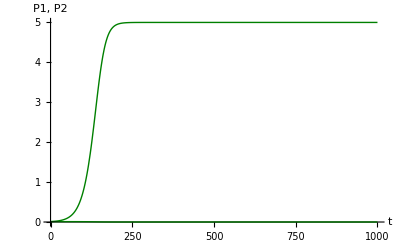

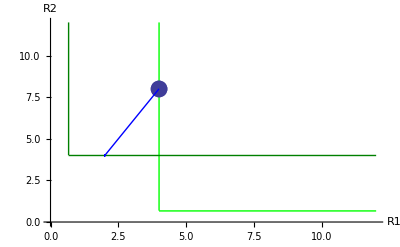

```mathematica
a=1;

k11=1;
k21=1;
q11=2;
q21=1;
vmax11=1;
vmax21=1;
m1=0.4;

k12=1;
k22=1;
q12=1;
q22=2;
vmax12=1;
vmax22=1;
m2=0.4;

rstar11=m1*k11/(vmax11/q11-m1);
rstar21=m1*k21/(vmax21/q21-m1);
rstar12=m2*k12/(vmax12/q12-m2);
rstar22=m2*k22/(vmax22/q22-m2);

tmax=1000;

r1in=4;
r2in=8;

sol=NDSolve[{
r1'[t]==a*(r1in-r1[t])-Min[vmax11/q11*r1[t]/(r1[t]+k11),vmax21/q21*r2[t]/(r2[t]+k21)]*p1[t]*q11-Min[vmax12/q12*r1[t]/(r1[t]+k12),vmax22/q22*r2[t]/(r2[t]+k22)]*p2[t]*q12,
r2'[t]==a*(r2in-r2[t])-Min[vmax11/q11*r1[t]/(r1[t]+k11),vmax21/q21*r2[t]/(r2[t]+k21)]*p1[t]*q21-Min[vmax12/q12*r1[t]/(r1[t]+k12),vmax22/q22*r2[t]/(r2[t]+k22)]*p2[t]*q22,
p1'[t]==Min[vmax11/q11*r1[t]/(r1[t]+k11),vmax21/q21*r2[t]/(r2[t]+k21)]*p1[t]-m1*p1[t],
p2'[t]==Min[vmax12/q12*r1[t]/(r1[t]+k12),vmax22/q22*r2[t]/(r2[t]+k22)]*p2[t]-m2*p2[t],
r1[0]==r1in,r2[0]==r2in,p1[0]==0.01,p2[0]==0.01},{r1,r2,p1,p2},{t,0,tmax}];

Plot[Evaluate[{p1[t],p2[t]}/.sol],{t,0,tmax},PlotStyle->{RGBColor[0,1,0],RGBColor[0,0.5,0]},PlotRange->All,AxesLabel->{"t","P1, P2"}]
ssplot=ListPlot[{{r1in,r2in}},PlotStyle->PointSize[0.03]];
zngiplot1=Plot[{10^5*(r1-rstar11)+rstar21,rstar21},{r1,rstar11,12},PlotRange->{{0,12},{0,12}},PlotStyle->RGBColor[0,1,0]];
zngiplot2=Plot[{10^5*(r1-rstar12)+rstar22,rstar22},{r1,rstar12,12},PlotRange->{{0,12},{0,12}},PlotStyle->RGBColor[0,0.5,0]];
rplot=ParametricPlot[Evaluate[{r1[t],r2[t]}/.sol],{t,0,tmax},PlotRange->{{0,12},{0,12}},PlotStyle->RGBColor[0,0,1],PlotPoints->100];
Show[ssplot,zngiplot1,zngiplot2,rplot,PlotRange->{{0,12},{0,12}},AxesLabel->{"R1","R2"}]
```

Species 2 (dark green) wins. It is a better competitor for resource 1 and worse for resource 2. In the above situation, resource 1 is the limiting resource, because it is at a lower input rate.

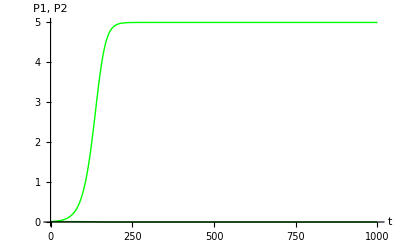

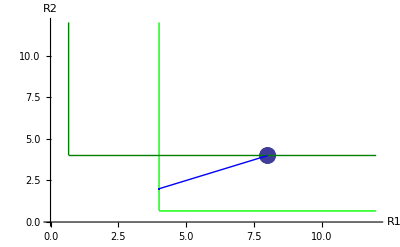

```mathematica
a=1;

k11=1;
k21=1;
q11=2;
q21=1;
vmax11=1;
vmax21=1;
m1=0.4;

k12=1;
k22=1;
q12=1;
q22=2;
vmax12=1;
vmax22=1;
m2=0.4;

rstar11=m1*k11/(vmax11/q11-m1);
rstar21=m1*k21/(vmax21/q21-m1);
rstar12=m2*k12/(vmax12/q12-m2);
rstar22=m2*k22/(vmax22/q22-m2);

tmax=1000;

r1in=8;
r2in=4;

sol=NDSolve[{
r1'[t]==a*(r1in-r1[t])-Min[vmax11/q11*r1[t]/(r1[t]+k11),vmax21/q21*r2[t]/(r2[t]+k21)]*p1[t]*q11-Min[vmax12/q12*r1[t]/(r1[t]+k12),vmax22/q22*r2[t]/(r2[t]+k22)]*p2[t]*q12,
r2'[t]==a*(r2in-r2[t])-Min[vmax11/q11*r1[t]/(r1[t]+k11),vmax21/q21*r2[t]/(r2[t]+k21)]*p1[t]*q21-Min[vmax12/q12*r1[t]/(r1[t]+k12),vmax22/q22*r2[t]/(r2[t]+k22)]*p2[t]*q22,
p1'[t]==Min[vmax11/q11*r1[t]/(r1[t]+k11),vmax21/q21*r2[t]/(r2[t]+k21)]*p1[t]-m1*p1[t],
p2'[t]==Min[vmax12/q12*r1[t]/(r1[t]+k12),vmax22/q22*r2[t]/(r2[t]+k22)]*p2[t]-m2*p2[t],
r1[0]==r1in,r2[0]==r2in,p1[0]==0.01,p2[0]==0.01},{r1,r2,p1,p2},{t,0,tmax}];

Plot[Evaluate[{p1[t],p2[t]}/.sol],{t,0,tmax},PlotStyle->{RGBColor[0,1,0],RGBColor[0,0.5,0]},PlotRange->All,AxesLabel->{"t","P1, P2"}]
ssplot=ListPlot[{{r1in,r2in}},PlotStyle->PointSize[0.03]];
zngiplot1=Plot[{10^5*(r1-rstar11)+rstar21,rstar21},{r1,rstar11,12},PlotRange->{{0,12},{0,12}},PlotStyle->RGBColor[0,1,0]];
zngiplot2=Plot[{10^5*(r1-rstar12)+rstar22,rstar22},{r1,rstar12,12},PlotRange->{{0,12},{0,12}},PlotStyle->RGBColor[0,0.5,0]];
rplot=ParametricPlot[Evaluate[{r1[t],r2[t]}/.sol],{t,0,tmax},PlotRange->{{0,12},{0,12}},PlotStyle->RGBColor[0,0,1],PlotPoints->100];
Show[ssplot,zngiplot1,zngiplot2,rplot,PlotRange->{{0,12},{0,12}},AxesLabel->{"R1","R2"}]
```

In this set up species 1 wins because resouce 2 is the limiting resource and species 1 is the better competitor on resource 1.

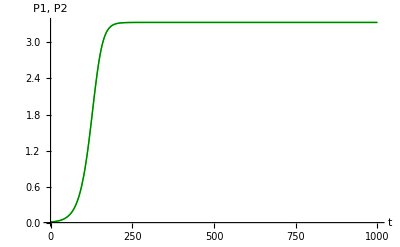

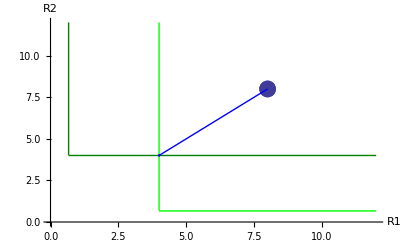

```mathematica
a=1;

k11=1;
k21=1;
q11=2;
q21=1;
vmax11=1;
vmax21=1;
m1=0.4;

k12=1;
k22=1;
q12=1;
q22=2;
vmax12=1;
vmax22=1;
m2=0.4;

rstar11=m1*k11/(vmax11/q11-m1);
rstar21=m1*k21/(vmax21/q21-m1);
rstar12=m2*k12/(vmax12/q12-m2);
rstar22=m2*k22/(vmax22/q22-m2);

tmax=1000;

r1in=8;
r2in=8;

sol=NDSolve[{
r1'[t]==a*(r1in-r1[t])-Min[vmax11/q11*r1[t]/(r1[t]+k11),vmax21/q21*r2[t]/(r2[t]+k21)]*p1[t]*q11-Min[vmax12/q12*r1[t]/(r1[t]+k12),vmax22/q22*r2[t]/(r2[t]+k22)]*p2[t]*q12,
r2'[t]==a*(r2in-r2[t])-Min[vmax11/q11*r1[t]/(r1[t]+k11),vmax21/q21*r2[t]/(r2[t]+k21)]*p1[t]*q21-Min[vmax12/q12*r1[t]/(r1[t]+k12),vmax22/q22*r2[t]/(r2[t]+k22)]*p2[t]*q22,
p1'[t]==Min[vmax11/q11*r1[t]/(r1[t]+k11),vmax21/q21*r2[t]/(r2[t]+k21)]*p1[t]-m1*p1[t],
p2'[t]==Min[vmax12/q12*r1[t]/(r1[t]+k12),vmax22/q22*r2[t]/(r2[t]+k22)]*p2[t]-m2*p2[t],
r1[0]==r1in,r2[0]==r2in,p1[0]==0.01,p2[0]==0.01},{r1,r2,p1,p2},{t,0,tmax}];

Plot[Evaluate[{p1[t],p2[t]}/.sol],{t,0,tmax},PlotStyle->{RGBColor[0,1,0],RGBColor[0,0.5,0]},PlotRange->All,AxesLabel->{"t","P1, P2"}]
ssplot=ListPlot[{{r1in,r2in}},PlotStyle->PointSize[0.03]];
zngiplot1=Plot[{10^5*(r1-rstar11)+rstar21,rstar21},{r1,rstar11,12},PlotRange->{{0,12},{0,12}},PlotStyle->RGBColor[0,1,0]];
zngiplot2=Plot[{10^5*(r1-rstar12)+rstar22,rstar22},{r1,rstar12,12},PlotRange->{{0,12},{0,12}},PlotStyle->RGBColor[0,0.5,0]];
rplot=ParametricPlot[Evaluate[{r1[t],r2[t]}/.sol],{t,0,tmax},PlotRange->{{0,12},{0,12}},PlotStyle->RGBColor[0,0,1],PlotPoints->100];
Show[ssplot,zngiplot1,zngiplot2,rplot,PlotRange->{{0,12},{0,12}},AxesLabel->{"R1","R2"}]
```

In this situation, they stably coexist because the resource inputs are equal.

### Can you change species parameters to show the founder control case?

-Graphics-

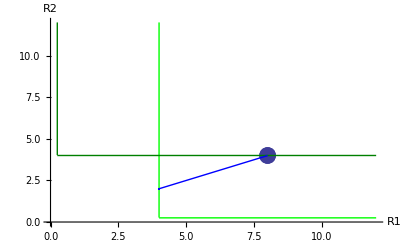

```mathematica
a=1;

k11=1;
k21=1;
q11=2;
q21=1;
vmax11=1;
vmax21=2;
m1=0.4;

k12=1;
k22=1;
q12=1;
q22=2;
vmax12=2;
vmax22=1;
m2=0.4;

rstar11=m1*k11/(vmax11/q11-m1);
rstar21=m1*k21/(vmax21/q21-m1);
rstar12=m2*k12/(vmax12/q12-m2);
rstar22=m2*k22/(vmax22/q22-m2);

tmax=1000;

r1in=8;
r2in=4;

sol=NDSolve[{
r1'[t]==a*(r1in-r1[t])-Min[vmax11/q11*r1[t]/(r1[t]+k11),vmax21/q21*r2[t]/(r2[t]+k21)]*p1[t]*q11-Min[vmax12/q12*r1[t]/(r1[t]+k12),vmax22/q22*r2[t]/(r2[t]+k22)]*p2[t]*q12,
r2'[t]==a*(r2in-r2[t])-Min[vmax11/q11*r1[t]/(r1[t]+k11),vmax21/q21*r2[t]/(r2[t]+k21)]*p1[t]*q21-Min[vmax12/q12*r1[t]/(r1[t]+k12),vmax22/q22*r2[t]/(r2[t]+k22)]*p2[t]*q22,
p1'[t]==Min[vmax11/q11*r1[t]/(r1[t]+k11),vmax21/q21*r2[t]/(r2[t]+k21)]*p1[t]-m1*p1[t],
p2'[t]==Min[vmax12/q12*r1[t]/(r1[t]+k12),vmax22/q22*r2[t]/(r2[t]+k22)]*p2[t]-m2*p2[t],
r1[0]==r1in,r2[0]==r2in,p1[0]==0.01,p2[0]==0.01},{r1,r2,p1,p2},{t,0,tmax}];

Plot[Evaluate[{p1[t],p2[t]}/.sol],{t,0,tmax},PlotStyle->{RGBColor[0,1,0],RGBColor[0,0.5,0]},PlotRange->All,AxesLabel->{"t","P1, P2"}]
ssplot=ListPlot[{{r1in,r2in}},PlotStyle->PointSize[0.03]];
zngiplot1=Plot[{10^5*(r1-rstar11)+rstar21,rstar21},{r1,rstar11,12},PlotRange->{{0,12},{0,12}},PlotStyle->RGBColor[0,1,0]];
zngiplot2=Plot[{10^5*(r1-rstar12)+rstar22,rstar22},{r1,rstar12,12},PlotRange->{{0,12},{0,12}},PlotStyle->RGBColor[0,0.5,0]];
rplot=ParametricPlot[Evaluate[{r1[t],r2[t]}/.sol],{t,0,tmax},PlotRange->{{0,12},{0,12}},PlotStyle->RGBColor[0,0,1],PlotPoints->100];
Show[ssplot,zngiplot1,zngiplot2,rplot,PlotRange->{{0,12},{0,12}},AxesLabel->{"R1","R2"}]
```

This is showing Founder Control because each species decreases the resource fastest that it is better at, thus which ever species starts off at an advantage will exclude the other.

## Bonus: Nutrient Recycling

### Modify the "One Resource, One Species, Fixed Yield" model to include nutrient recycling, so that a fraction (0<=ϕ<=1) of each cell is returned to the available nutrient pool upon death. What are your equations? What happens to the equilibrium biomass and nutrient concentration as a function of ϕ? Does nutrient recycling affect the outcome of competition for one resource? Note: to make a ϕ, type esc-f-esc!